## Chapter 7 : Data Exploration

## 7.1 Wolfram Data Repository

```mathematica
URLRead["https://datarepository.wolframcloud.com/"]
```

HTTPResponse[…]

### 7.1.1 Wolfram Data Repository Website

### 7.1.2 Selecting a Category

## 7.2 Extracting Data from the Wolfram Data Repository

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]
```

ResourceObject[…]

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["Properties"]
```

{AllVersions,AutoUpdate,Categories,ContentElementLocations,ContentElements,ContentSize,ContentTypes,ContributorInformation,DatedElementVersions,DefaultContentElement,Description,Details,Documentation,DocumentationLink,DOI,DownloadedVersion,ExampleNotebook,ExampleNotebookObject,Format,InformationElements,Keywords,LatestUpdate,Name,Originator,Properties,PublisherUUID,ReleaseDate,RepositoryLocation,ResourceLocations,ResourceType,SeeAlso,ShortName,SourceMetadata,UUID,Version,VersionInformation,VersionsAvailable,WolframLanguageVersionRequired}

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["ExampleNotebook"]
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["ExampleNotebookObject"]
```

CloudObject[https://www.wolframcloud.com/obj/5e59b79e-d95e-4f6f-a7c8-f1276ba17be2]

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["Documentation"]
```

URL[https://datarepository.wolframcloud.com/resources/b7f632f7-9c5f-4ad4-a73e-446cc2656f64/]

### 7.2.1 Accessing Data Inside Mathematica

```mathematica
ResourceData[ResourceObject["Sample Data: Fisher's Irises"]]
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["ContentElements"]
```

{ColumnDescriptions,ColumnTypes,Content,DataType,Dimensions,ObservationCount,RawData,Source,TrainingData,TestData}

```mathematica
ResourceData[ResourceObject["Sample Data: Fisher's Irises"],"ColumnTypes"]
```

{Numeric,Numeric,Numeric,Numeric,Categorical}

```mathematica
Column[ResourceData[ResourceObject["Sample Data: Fisher's Irises"],#]&/@{"ColumnDescriptions","Dimensions","Source"}]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}
{150,4}
Fisher,R.A. "The use of multiple measurements in taxonomic problems" Annual Eugenics, 7, Part II, 179-188 (1936); also in "Contributions to Mathematical Statistics" (John Wiley, NY, 1950).

### 7.2.2 Data Observation and Querying

```mathematica
fisher=ResourceData[ResourceObject["Sample Data: Fisher's Irises"]];
```

```mathematica
fisher[GroupBy["Species"]]
```

```mathematica
Query[GroupBy[Key["Species"]->KeyTake[{"SepalLength","SepalWidth","PetalLength","PetalWidth"}]]][fisher]
```

```mathematica
Query[AssociationThread[Range[Length@#]->Range[Length@#]]][fisher]&[fisher]
```

```mathematica
fisher[Counts,"Species"]
```

```mathematica
Query[GroupBy[Key["Species"]->KeyTake[{"SepalLength","SepalWidth","PetalLength","PetalWidth"}]],Mean][fisher]
```

```mathematica
Query[Mean][fisher[[All,2;;5]]]
```

## 7.4 Descriptive Statistics

```mathematica
stats[data_]:=
{{#[{"Max: ",Max@data}]},
{#[{"Min: ",Min@data}]},
{#[{"Mean: ",Mean@data}]},
{#[{"Median: ",Median@data}]},
{#[{"1st quartile: ",Quantile[data,0.25]}]},
{#[{"3rd quartile: ",Quantile[data,0.75]}]}
}&[Row]
```

```mathematica
{{#1,#2,#3,#4},{fisher[stats,#1],fisher[stats,#2],fisher[stats,#3],fisher[stats,#4]}}&["SepalLength","SepalWidth","PetalLength","PetalWidth"]//Grid
```

SepalLength | SepalWidth | PetalLength | PetalWidth
 |  |  |

```mathematica
TabView[{#1->fisher[stats,#1],#2->fisher[stats,#2],#3->fisher[stats,#3],#4->fisher[stats,#4]},ControlPlacement->Left]&["SepalLength","SepalWidth","PetalLength","PetalWidth"]
```

1234

### 7.4.1 Table and Grid Formats

```mathematica
Short[Values[Nest[Normal,fisher,2]]]
{sLall,sWall,pLall,pWall}=%[[All,#]]&/@{2,3,4,5};
```

{{setosa,5.1 cm,3.5 cm,1.4 cm,0.2 cm},«148»,{virginica,5.9 cm,3. cm,5.1 cm,1.8 cm}}

```mathematica
{Max[#],Min[#],Median[#],Mean[#],Variance[#],StandardDeviation[#],Skewness[#],Kurtosis[#],Quantile[#,0.25],Quantile[#,.75]}&/@{sLall,sWall,pLall,pWall};
descriptiveStats=%;
```

```mathematica
tableHeads={Style["Sepal Length",#1,ColorData["HTML"]["Maroon"],#2,#3],Style["Sepal Width",#1,ColorData["HTML"]["YellowGreen"],#2,#3],Style["Petal Length",#1,ColorData["HTML"]["SteelBlue"],#2,#3],Style["Petal Width",#1,ColorData["HTML"]["Orange"],#2,#3]}&["Title",Italic,20];
tableRows={Style["Max",#1,#2],Style["Min",#1,#2],Style["Median",#1,#2],Style["Mean",#1,#2],Style["Variance",#1,#2],Style["Standard\n Deviation",#1,#2],Style["Skewness",#1,#2],Style["Kurtosis",#1,#2],Style["1st quartile",#1,#2],Style["3rd quartile",#1,#2]}&["Text",Italic];TableForm[descriptiveStats,TableHeadings->{tableHeads,tableRows}]
```

| Max | Min | Median | Mean | Variance | Standard
 Deviation | Skewness | Kurtosis | 1st quartile | 3rd quartile
Sepal Length | 7.9 cm | 4.3 cm | 5.8 cm | 5.84333 cm | 0.685694 cm^2 | 0.828066 cm | 0.311753 | 2.42643 | 5.1 cm | 6.4 cm
Sepal Width | 4.4 cm | 2. cm | 3. cm | 3.05733 cm | 0.189979 cm^2 | 0.435866 cm | 0.315767 | 3.18098 | 2.8 cm | 3.3 cm
Petal Length | 6.9 cm | 1. cm | 4.35 cm | 3.758 cm | 3.11628 cm^2 | 1.7653 cm | -0.272128 | 1.60446 | 1.6 cm | 5.1 cm
Petal Width | 2.5 cm | 0.1 cm | 1.3 cm | 1.19933 cm | 0.581006 cm^2 | 0.762238 cm | -0.101934 | 1.66393 | 0.3 cm | 1.8 cm

```mathematica
Transpose[Prepend[descriptiveStats,tableRows]];
{" ",Style["Sepal Length",#1,ColorData["HTML"]["Maroon"],#2,#3],Style["Sepal Width",#1,ColorData["HTML"]["YellowGreen"],#2,#3],Style["Petal Length",#1,ColorData["HTML"]["SteelBlue"],#2,#3],Style["Petal Width",#1,ColorData["HTML"]["Orange"],#2,#3]}&["Title",Italic,20];
newTable=Prepend[%%,%];
```

```mathematica
Grid[newTable,ItemSize->{{None,Scaled[0.11],Scaled[0.11],Scaled[0.11]}},Background->{{LightGray},None},Dividers->{{False},{1,2,3,4,5,6,7,8,9,10,11->True,-2->Blue}},Alignment->Center]
```

| Sepal Length | Sepal Width | Petal Length | Petal Width
Max | 7.9 cm | 4.4 cm | 6.9 cm | 2.5 cm
Min | 4.3 cm | 2. cm | 1. cm | 0.1 cm
Median | 5.8 cm | 3. cm | 4.35 cm | 1.3 cm
Mean | 5.84333 cm | 3.05733 cm | 3.758 cm | 1.19933 cm
Variance | 0.685694 cm^2 | 0.189979 cm^2 | 3.11628 cm^2 | 0.581006 cm^2
Standard
 Deviation | 0.828066 cm | 0.435866 cm | 1.7653 cm | 0.762238 cm
Skewness | 0.311753 | 0.315767 | -0.272128 | -0.101934
Kurtosis | 2.42643 | 3.18098 | 1.60446 | 1.66393
1st quartile | 5.1 cm | 2.8 cm | 1.6 cm | 0.3 cm
3rd quartile | 6.4 cm | 3.3 cm | 5.1 cm | 1.8 cm

```mathematica
Shallow[Values[Nest[Normal,fisher,2]],1]
```

{«150»}

```mathematica
Shallow[Cases[%,{"versicolor",__}],1]
{sLVersi,sWVersi,pLVersi,pWVersi}=%[[All,#]]&/@{2,3,4,5};
```

{«50»}

```mathematica
tableRows;
{Max[#],Min[#],Median[#],Mean[#],Variance[#],StandardDeviation[#],Skewness[#],Kurtosis[#],Quantile[#,0.25],Quantile[#,.75]}&/@{sLVersi,sWVersi,pLVersi,pWVersi};
descriptiveStats2=Prepend[%,%%];
Transpose[descriptiveStats2];
{Style["Versicolor","Text",Red,Italic,20],Style["Sepal Length",#1,ColorData["HTML"]["Maroon"],#2,#3],Style["Sepal Width",#1,ColorData["HTML"]["YellowGreen"],#2,#3],Style["Petal Length",#1,ColorData["HTML"]["SteelBlue"],#2,#3],Style["Petal Width",#1,ColorData["HTML"]["Orange"],#2,#3]}&["Title",Italic,20];
newTable2=Prepend[%%,%];
```

```mathematica
Grid[newTable2,ItemSize->{{None,Scaled[0.11],Scaled[0.11],Scaled[0.11]}},Background->{{LightGray},None},Dividers->{{False},{1,2,3,4,5,6,7,8,9,10,11->True,-2->Blue}},Alignment->Center]
```

Versicolor | Sepal Length | Sepal Width | Petal Length | Petal Width
Max | 7. cm | 3.4 cm | 5.1 cm | 1.8 cm
Min | 4.9 cm | 2. cm | 3. cm | 1. cm
Median | 5.9 cm | 2.8 cm | 4.35 cm | 1.3 cm
Mean | 5.936 cm | 2.77 cm | 4.26 cm | 1.326 cm
Variance | 0.266433 cm^2 | 0.0984694 cm^2 | 0.220816 cm^2 | 0.0391061 cm^2
Standard
 Deviation | 0.516171 cm | 0.313798 cm | 0.469911 cm | 0.197753 cm
Skewness | 0.10219 | -0.351867 | -0.588159 | -0.0302363
Kurtosis | 2.40117 | 2.55173 | 2.9256 | 2.51217
1st quartile | 5.6 cm | 2.5 cm | 4. cm | 1.2 cm
3rd quartile | 6.3 cm | 3. cm | 4.6 cm | 1.5 cm

## 7.5 Dataset Visualisation

```mathematica
fisher[GroupBy["Species"],DistributionChart[#,PlotTheme->"Classic",PlotLabel->"PetalLength cm",GridLines->Automatic]&,"PetalLength"]
```

```mathematica
fisher[GroupBy["Species"],BoxWhiskerChart[#,"Outliers",PlotTheme->"Detailed",ChartLabels->Placed[{"SepalLength cm"},Above],BarOrigin->Right,ChartStyle->Blue]&,"SepalLength"]
```

```mathematica
fisher[GroupBy["Species"],Labeled[Histogram[#,ColorFunction->(Hue[3/5,2/3,#]&)],{Rotate["Frequency",90 Degree],"SepalWidth cm"},{Left,Bottom}]&,"SepalWidth"]
```

```mathematica
fisher[GroupBy["Species"],Labeled[ListPlot[{#,#}],{Rotate["Sepal width cm",90 Degree],"Sepal length cm"},{Left,Bottom}]&,{"SepalLength","SepalWidth"}]
```

### 7.5.1 Data Outside Dataset Format

```mathematica
Short[ResourceData[ResourceObject["Sample Data: Fisher's Irises"],"RawData"]]
```

{<|Species→setosa,SepalLength→5.1 cm,SepalWidth→3.5 cm,PetalLength→1.4 cm,PetalWidth→0.2 cm|>,«148»,<|Species→virginica,«3»,P…th→1.8 cm|>}

```mathematica
Short[Normal[Values[%]]]
```

{{setosa,5.1 cm,3.5 cm,1.4 cm,0.2 cm},{setosa,4.9 cm,3. cm,1.4 cm,0.2 cm},{setosa,4.7 cm,3.2 cm,1.3 cm,0.2 cm},«144»,{virginica,6.5 cm,3. cm,5.2 cm,2. cm},{virginica,6.2 cm,3.4 cm,5.4 cm,2.3 cm},{virginica,5.9 cm,3. cm,5.1 cm,1.8 cm}}

```mathematica
Short[iris=MapAt[QuantityMagnitude,%,{All,2;;5}]]
```

{{setosa,5.1,3.5,1.4,0.2},{setosa,4.9,3.,1.4,0.2},«147»,{virginica,5.9,3.,5.1,1.8}}

### 7.5.2 2D and 3D Plots

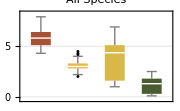
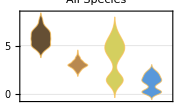

```mathematica
Row[{BoxWhiskerChart[{iris[[All,#1]],iris[[All,#2]],iris[[All,#3]],iris[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"SandyTerrain",PlotLabel->"All Species",GridLines->Automatic,ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],ImageSize->Small],DistributionChart[{iris[[All,#1]],iris[[All,#2]],iris[[All,#3]],iris[[All,#4]]},PlotRange->Automatic,FrameTicks->True,ChartStyle->"SouthwestColors",PlotLabel->"All Species",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],PlotTheme->"Detailed",GridLines->Automatic,ImageSize->Small]}]&[2,3,4,5]
```

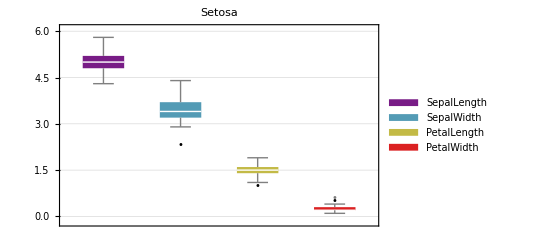
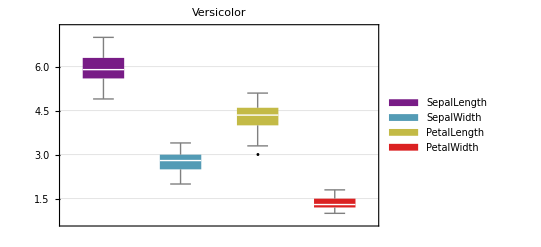
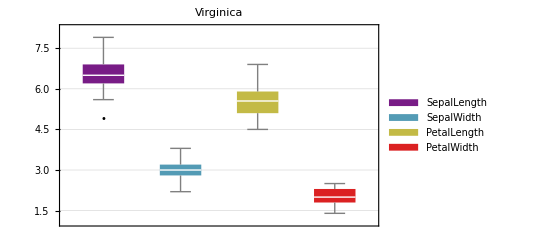

```mathematica
Short[setosa=Cases[iris,{"setosa",__}]];
Short[versi=Cases[iris,{"versicolor",__}]];
Short[virgin=Cases[iris,{"virginica",__}]];
Column@{BoxWhiskerChart[{setosa[[All,#1]],setosa[[All,#2]],setosa[[All,#3]],setosa[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"Rainbow",PlotLabel->"Setosa",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],GridLines->Automatic],BoxWhiskerChart[{versi[[All,#1]],versi[[All,#2]],versi[[All,#3]],versi[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"Rainbow",PlotLabel->"Versicolor",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],GridLines->Automatic],BoxWhiskerChart[{virgin[[All,#1]],virgin[[All,#2]],virgin[[All,#3]],virgin[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"Rainbow",PlotLabel->"Virginica",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],GridLines->Automatic]
}&[2,3,4,5]
```

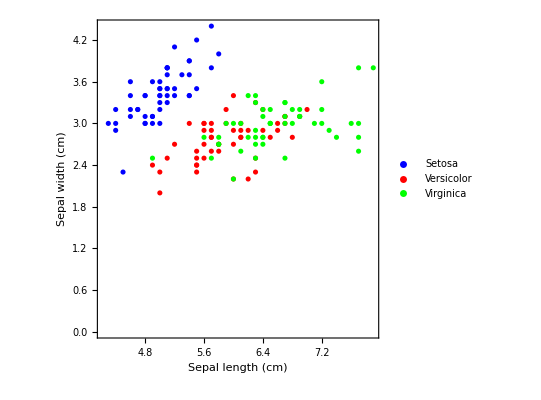

```mathematica
ListPlot[{setosa[[All,{2,3}]],versi[[All,{2,3}]],virgin[[All,{2,3}]]},FrameTicks->All,Frame->True,AspectRatio->1,PlotStyle->{Blue,Red,Green},FrameLabel->{Style["Sepal length (cm)",FontSize->20],Style["Sepal width (cm)",FontSize->20]},PlotLegends->{"Setosa","Versicolor","Virginica"}]
```

```mathematica
ListPointPlot3D[{setosa[[All,{2,3,4}]],versi[[All,{2,3,4}]],virgin[[All,{2,3,4}]]},Ticks->All,AspectRatio->1,PlotStyle->{Blue,Red,Green},AxesLabel->{Style["Sepal length cm",FontSize->13],Style["Sepal width cm",FontSize->13],Style["Petal Length cm",FontSize->13]},PlotLegends->{"Setosa","Versicolor","Virginica"},PlotTheme->"Detailed",ViewPoint->{0,-3,3}]
```

-Graphics3D-

```mathematica
Clear[fisher]
DeleteObject[ResourceObject["Sample Data: Fisher's Irises"]]
```